```mathematica
data2 = {{-0.2,-1.15842418},{-0.17894737,-1.16142061},{-0.15789474,-1.16423061},{-0.13684211,-1.16682315},{-0.11578947,-1.16916309},{-0.09473684,-1.17121068},{-0.07368421,-1.17292081},{-0.05263158,-1.17424233},{-0.03157895,-1.17511705},{-0.01052632,-1.17547874},{0.01052632,-1.17525189},{0.03157895,-1.17435036},{0.05263158,-1.17267563},{0.07368421,-1.17011474},{0.09473684,-1.16653779},{0.11578947,-1.16179489},{0.13684211,-1.15571242},{0.15789474,-1.1480882},{0.17894737,-1.1386857},{0.2,-1.12722727}}
```

{{-0.2,-1.15842},{-0.178947,-1.16142},{-0.157895,-1.16423},{-0.136842,-1.16682},{-0.115789,-1.16916},{-0.0947368,-1.17121},{-0.0736842,-1.17292},{-0.0526316,-1.17424},{-0.031579,-1.17512},{-0.0105263,-1.17548},{0.0105263,-1.17525},{0.031579,-1.17435},{0.0526316,-1.17268},{0.0736842,-1.17011},{0.0947368,-1.16654},{0.115789,-1.16179},{0.136842,-1.15571},{0.157895,-1.14809},{0.178947,-1.13869},{0.2,-1.12723}}

```mathematica
wave = 3.33565*10^-11
```

3.33565×10^-11

```mathematica
joulem = 435.974
```

435.974

```mathematica
redmass = 1.67349112*10^-27
```

1.67349×10^-27

```mathematica
ifun2 = Interpolation[data2]
```

InterpolatingFunction[{{-0.2, 0.2}}, <>]

```mathematica
ifun2'
```

InterpolatingFunction[{{-0.2, 0.2}}, <>]

```mathematica
%78'
```

InterpolatingFunction[{{-0.2, 0.2}}, <>]

```mathematica
%79[-0.007630240605500548]
```

1.35463

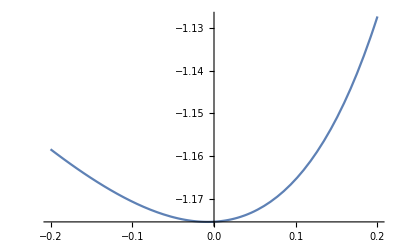

```mathematica
Plot[ifun2[x],{x,-0.2,0.2}]
```

```mathematica
FindMinimum[ifun2[x],x]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.17548,{x→-0.00763024}}

```mathematica
1.3546290304564734* joulem
```

590.583

```mathematica
1177.76/590.5830369242306
```

1.99423

```mathematica
tmdata = {{-0.2,-1.06641304},{-0.17894737,-1.06924179},{-0.15789474,-1.07154836},{-0.13684211,-1.07349485},{-0.11578947,-1.07510482},{-0.09473684,-1.07640188},{-0.07368421,-1.07751603},{-0.05263158,-1.07814867},{-0.03157895,-1.07857431},{-0.01052632,-1.07874074},{0.01052632,-1.07872238},{0.03157895,-1.07830953},{0.05263158,-1.07705033},{0.07368421,-1.07516901},{0.09473684,-1.07299594},{0.11578947,-1.0701368},{0.13684211,-1.06615127},{0.15789474,-1.06109564},{0.17894737,-1.05461028},{0.2,-1.04558401}}
```

{{-0.2,-1.06641},{-0.178947,-1.06924},{-0.157895,-1.07155},{-0.136842,-1.07349},{-0.115789,-1.0751},{-0.0947368,-1.0764},{-0.0736842,-1.07752},{-0.0526316,-1.07815},{-0.031579,-1.07857},{-0.0105263,-1.07874},{0.0105263,-1.07872},{0.031579,-1.07831},{0.0526316,-1.07705},{0.0736842,-1.07517},{0.0947368,-1.073},{0.115789,-1.07014},{0.136842,-1.06615},{0.157895,-1.0611},{0.178947,-1.05461},{0.2,-1.04558}}

```mathematica
tmifun = Interpolation[tmdata]
```

InterpolatingFunction[{{-0.2, 0.2}}, <>]

```mathematica
tmifun'
```

InterpolatingFunction[{{-0.2, 0.2}}, <>]

```mathematica
%87'
```

InterpolatingFunction[{{-0.2, 0.2}}, <>]

```mathematica
%88[-0.0007080379936242091]
```

0.637588

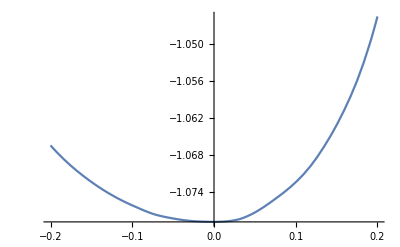

```mathematica
Plot[tmifun[x],{x,-0.2,0.2}]
```

```mathematica
FindMinimum[tmifun[x],x]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.07877,{x→-0.000708038}}

```mathematica
k = 0.6375877892782474*2
```

1.27518

```mathematica
k * joulem
```

555.943

```mathematica
newk = k * joulem
```

555.943

```mathematica
x = newk / redmass
```

3.32206×10^29

```mathematica
Sqrt[x]
```

5.76373×10^14

```mathematica
newx = Sqrt[x]
```

5.76373×10^14

```mathematica
Hz = newx * (1/(2*Pi))
```

9.17326×10^13

```mathematica
Hz * wave
```

3059.88